## Testing the signature formalism for the ^163Lu fit

## The fit uses the approach where TSD4 shares the same coupling scheme as the other three bands

the formulas for the first three bands are as follows:

TSD1 is the ground state with the coupling scheme j=13/2

TSD2 is the ground state at the same coupling scheme, but a different spin sequence. TSD2 is considered the signature partner band of TSD1

TSD3 is the 1-phonon excited state, built on top of TSD2, and it is in the same coupling scheme j=13/2

TSD4 is the 0-(or 1-)phonon excited band of this nucleus, built on top of TSD1 (with an excited phonon or just the ground state). It is the parity partner band of TSD2, considered from the parity symmetry.

## Formulas

```mathematica
IF[I_]:=1/(2I);
B[I_,j_,A1_,A2_,A3_,V_,γ_]:=-(((2I-1)(A3-A1)+2j*A1)*((2I-1)(A2-A1)+2j*A1)+8A2*A3*I*j+((2j-1)(A3-A1)+2I*A1+V(2j-1)/(j(j+1))√3(√3 Cos[γ*π/180]+Sin[γ*π/180]))*((2j-1)(A2-A1)+2I*A1+V(2j-1)/(j(j+1))2 √3 Sin[γ*π/180]));
C1[I_,j_,A1_,A2_,A3_,V_,γ_]:=(((2I-1)(A3-A1)+2j*A1)*((2j-1)(A3-A1)+2I*A1+V*(2j-1)/(j(j+1))√3(√3 Cos[γ*π/180]+Sin[γ*π/180]))-4I*j*A3^2)*(((2I-1)(A2-A1)+2j*A1)*((2j-1)(A2-A1)+2I*A1+V*(2j-1)/(j(j+1))2 √3 Sin[γ*π/180])-4I*j*A2^2);
HMin[I_,j_,A1_,A2_,A3_,V_,γ_]:=(A2+A3)/2(I+j)+A1(I-j)^2-V*(2j-1)/(j+1)Sin[γ*π/180+π/6];
Omega1[I_,j_,A1_,A2_,A3_,V_,γ_]:=√(1/2(-B[I,j,A1,A2,A3,V,γ]-(B[I,j,A1,A2,A3,V,γ]^2-4C1[I,j,A1,A2,A3,V,γ])^(1/2)));
Omega2[I_,j_,A1_,A2_,A3_,V_,γ_]:=√(1/2(-B[I,j,A1,A2,A3,V,γ]+(B[I,j,A1,A2,A3,V,γ]^2-4C1[I,j,A1,A2,A3,V,γ])^(1/2)));
EWobb[n1_,n2_,I_,j_,A1_,A2_,A3_,V_,γ_]:=HMin[I,j,A1,A2,A3,V,γ]+Omega1[I,j,A1,A2,A3,V,γ](n1+1/2)+Omega2[I,j,A1,A2,A3,V,γ](n2+1/2);
TSD1[I_,A1_,A2_,A3_,V_,γ_]:=EWobb[0,0,I,6.5,A1,A2,A3,V,γ]-EWobb[0,0,6.5,6.5,A1,A2,A3,V,γ];
TSD2[I_,A1_,A2_,A3_,V_,γ_]:=EWobb[0,0,I,6.5,A1,A2,A3,V,γ]-EWobb[0,0,6.5,6.5,A1,A2,A3,V,γ];
TSD3[I_,A1_,A2_,A3_,V_,γ_]:=EWobb[1,0,I-1,6.5,A1,A2,A3,V,γ]-EWobb[0,0,6.5,6.5,A1,A2,A3,V,γ];
TSD4[I_,A1_,A2_,A3_,V_,γ_]:=EWobb[1,0,I-1,6.5,A1,A2,A3,V,γ]-EWobb[0,0,6.5,6.5,A1,A2,A3,V,γ];
TSD410[I_,A1_,A2_,A3_,V_,γ_]:=EWobb[1,0,I-1,6.5,A1,A2,A3,V,γ]-EWobb[0,0,6.5,6.5,A1,A2,A3,V,γ];
(*TSD410[I_,A1_,A2_,A3_,V_,γ_]:=EWobb[1,0,I-1,6.5,A1,A2,A3,V,γ]-EWobb[0,0,6.5,6.5,A1,A2,A3,V,γ];*)
```

## Calculations

```mathematica
spin1={8.5,10.5,12.5,14.5,16.5,18.5,20.5,22.5,24.5,26.5,28.5,30.5,32.5,34.5,36.5,38.5,40.5,42.5,44.5,46.5,48.5};
spin2={13.5,15.5,17.5,19.5,21.5,23.5,25.5,27.5,29.5,31.5,33.5,35.5,37.5,39.5,41.5,43.5,45.5};
spin3={16.5,18.5,20.5,22.5,24.5,26.5,28.5,30.5,32.5,34.5,36.5,38.5,40.5,42.5};
spin4={23.5,25.5,27.5,29.5,31.5,33.5,35.5,37.5,39.5,41.5};
```

```mathematica
tsd1={0.1966,0.4597,0.7746,1.1609,1.6112,2.1265,2.7051,3.3441,4.0411,4.7937,5.5992,6.457,7.3667,8.3293,9.3458,10.4169,11.5431,12.7224,13.9491,15.2181,16.5221};
tsd2={1.3394,1.7467,2.2184,2.7527,3.3484,4.003,4.7143,5.4805,6.3004,7.1733,8.0998,9.08,10.1147,11.2036,12.3466,13.5441,14.7911};
tsd3={2.1237,2.6293,3.1973,3.8243,4.5094,5.2506,6.0465,6.8963,7.7988,8.7546,9.7638,10.8268,11.9392,13.0861};
tsd4={4.58,5.2251,5.9273,6.6819,7.4919,8.3573,9.2778,10.2535,11.2851,12.3701};
```

```mathematica
spinTSD1=N[25/2];
spinTSD2=N[31/2];
spinTSD3=N[37/2];
spinTSD4=N[51/2];
j=13/2;
```

```mathematica
printer[spins_,tsd_,A1_,A2_,A3_,V_,γ_]:=Table[{spins[[i]],tsd[spins[[i]],A1,A2,A3,V,γ]},{i,1,Length[spins]}];
```

## The fit parameters (obtained from C++ implementation)

## Standard approach

```mathematica
i1=73;i2=68;i3=3;v=8.1;γ=15;
```

## (0,0) - approach

```mathematica
i100=77;i200=47;i300=3;v00=7.1;γ00=15;
```

## (1,0) - approach

```mathematica
i110=73;i210=68;i310=3;v10=8.1;γ10=15;
```

## Replacing ONLY the fit parameters should make the implementation change properly

## Output the energies for consistency (compare with C++ numerical output)

```mathematica
shower[spins_,tsd_]:=Do[Print[printer[spins,tsd,IF[i1],IF[i2],IF[i3],v,γ][[i]]],{i,1,Length[spins]}];
```

## RMS calculation

```mathematica
rms[a1_,a2_,a3_,v_,γ_]:=Sqrt[1/63(Sum[(tsd1[[i]]-TSD1[spin1[[i]],a1,a2,a3,v,γ])^2,{i,1,Length[spin1]}]+Sum[(tsd2[[i]]-TSD2[spin2[[i]],a1,a2,a3,v,γ])^2,{i,1,Length[spin2]}]+Sum[(tsd3[[i]]-TSD3[spin3[[i]],a1,a2,a3,v,γ])^2,{i,1,Length[spin3]}]+Sum[(tsd4[[i]]-TSD4[spin4[[i]],a1,a2,a3,v,γ])^2,{i,1,Length[spin4]}])];
```

```mathematica
Print[Style[StringTemplate["E_RMS=``"][rms[IF[i1],IF[i2],IF[i3],v,γ]],Red,20,Bold,FontFamily->"Times New Roman"]]
```

E_RMS=0.138381

```mathematica
Print[Style[StringTemplate["E_RMS(0,0)=``"][rms[IF[i100],IF[i200],IF[i300],v00,γ00]],Red,20,Bold,FontFamily->"Times New Roman"]]
```

E_RMS(0,0)=0.381505

```mathematica
Print[Style[StringTemplate["E_RMS(1,0)=``"][rms[IF[i110],IF[i210],IF[i310],v10,γ10]],Red,20,Bold,FontFamily->"Times New Roman"]]
```

E_RMS(1,0)=0.138381

## Test any RMS value in terms of the fit parameters

```mathematica
Print[Style[StringTemplate["E_RMS=``"][rms[IF[77],IF[32],IF[50],2.1,16]],Blue,24,Bold,Italic,FontFamily->"Times New Roman"]]
```

E_RMS=2.51486

## TSD1

```mathematica
shower[spin1,TSD1]
```

{8.5,0.255051}

{10.5,0.561724}

{12.5,0.920924}

{14.5,1.3332}

{16.5,1.7989}

{18.5,2.31829}

{20.5,2.89155}

{22.5,3.51882}

{24.5,4.2002}

{26.5,4.9358}

{28.5,5.72567}

{30.5,6.56987}

{32.5,7.46846}

{34.5,8.42147}

{36.5,9.42895}

{38.5,10.4909}

{40.5,11.6074}

{42.5,12.7784}

{44.5,14.004}

{46.5,15.2842}

{48.5,16.6189}

## TSD2

```mathematica
shower[spin2,TSD2]
```

{13.5,1.1204}

{15.5,1.55935}

{17.5,2.05187}

{19.5,2.59818}

{21.5,3.19842}

{23.5,3.85274}

{25.5,4.56122}

{27.5,5.32394}

{29.5,6.14097}

{31.5,7.01236}

{33.5,7.93816}

{35.5,8.9184}

{37.5,9.95312}

{39.5,11.0423}

{41.5,12.1861}

{43.5,13.3844}

{45.5,14.6373}

## TSD3

```mathematica
shower[spin3,TSD3]
```

{16.5,2.12132}

{18.5,2.65026}

{20.5,3.23115}

{22.5,3.86449}

{24.5,4.55064}

{26.5,5.2899}

{28.5,6.08249}

{30.5,6.92861}

{32.5,7.82841}

{34.5,8.78202}

{36.5,9.78957}

{38.5,10.8511}

{40.5,11.9668}

{42.5,13.1366}

## TSD4

```mathematica
shower[spin4,TSD4]
```

{23.5,4.20095}

{25.5,4.91362}

{27.5,5.67951}

{29.5,6.49885}

{31.5,7.37179}

{33.5,8.29848}

{35.5,9.27905}

{37.5,10.3136}

{39.5,11.4022}

{41.5,12.545}

## Plotting the energies based on the actual parameter values.

```mathematica
plot[spins_,band_,I1_,I2_,I3_,V_,γ_]:=Plot[band[x,IF[I1],IF[I2],IF[I3],V,γ],{x,spins[[1]],spins[[Length[spins]]]},AspectRatio->0.7,Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],PlotStyle->{Thick,Red},FrameLabel->{"I [ℏ]","E [MeV]"},LabelStyle->{18,Bold,Black,FontFamily->"Times New Roman"},Epilog->Inset[Style[StringTemplate["``"][band],Black,Bold,20,Italic,FontFamily->"Times New Roman"],Scaled[{0.25,0.75}]]];
showCombo[spins_,tsd_,band_,I1_,I2_,I3_,V_,γ_]:=Show[plot[spins,band,I1,I2,I3,V,γ],ListPlot[Table[{spins[[i]],tsd[[i]]},{i,1,Length[spins]}],PlotStyle->Black,PlotMarkers->{Automatic, 8}]];
```

## Show the plots in final form (depends on the fit parameters)

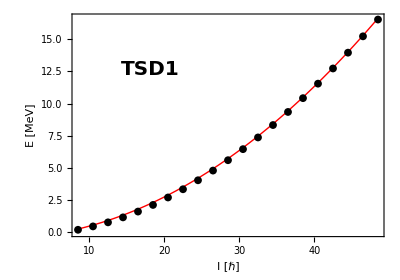

```mathematica
showCombo[spin1,tsd1,TSD1,i1,i2,i3,v,γ]
```

```mathematica
Export["/Users/basavyr/Library/Mobile Documents/com~apple~CloudDocs/Work/Pipeline/DFT/163Lu-New-TSD4-Formalism/Reports/SIGNATURE_FORMALISM/tsd1_signature.png",showCombo[spin1,tsd1,TSD1,i1,i2,i3,v,γ]];
```

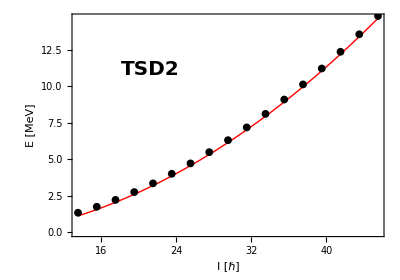

```mathematica
showCombo[spin2,tsd2,TSD2,i1,i2,i3,v,γ]
```

```mathematica
Export["/Users/basavyr/Library/Mobile Documents/com~apple~CloudDocs/Work/Pipeline/DFT/163Lu-New-TSD4-Formalism/Reports/SIGNATURE_FORMALISM/tsd2_signature.png",showCombo[spin2,tsd2,TSD2,i1,i2,i3,v,γ]];
```

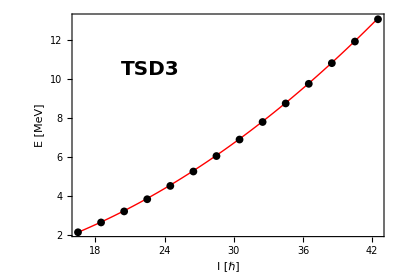

```mathematica
showCombo[spin3,tsd3,TSD3,i1,i2,i3,v,γ]
```

```mathematica
Export["/Users/basavyr/Library/Mobile Documents/com~apple~CloudDocs/Work/Pipeline/DFT/163Lu-New-TSD4-Formalism/Reports/SIGNATURE_FORMALISM/tsd3_signature.png",showCombo[spin3,tsd3,TSD3,i1,i2,i3,v,γ]];
```

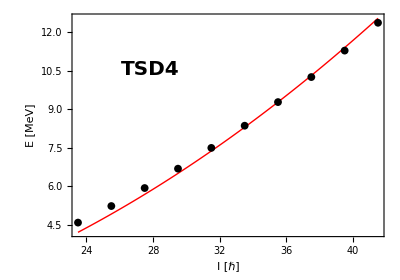

```mathematica
showCombo[spin4,tsd4,TSD4,i1,i2,i3,v,γ]
```

```mathematica
Export["/Users/basavyr/Library/Mobile Documents/com~apple~CloudDocs/Work/Pipeline/DFT/163Lu-New-TSD4-Formalism/Reports/SIGNATURE_FORMALISM/tsd4_signature.png",showCombo[spin4,tsd4,TSD4,i1,i2,i3,v,γ]];
```

## Contour Plot for the energy function

### Evaluated at the proper obtained fit parameters (which are given as input)

```mathematica
i1=52;i2=32;i3=48;v=9.1;γ=15;
```

```mathematica
Hen[I_,θ_,φ_,A1_,A2_,A3_,V_,γ_]:=I/2(A1+A2)+A3*I^2+I(I-1/2)Sin[θ*π/180]^2(A1*Cos[φ*π/180]^2+A2*Sin[φ*π/180]^2-A3)+j/2(A2+A3)+A1*j^2-2A1*I*j*Sin[θ*π/180]-V*(2j-1)/(j+1)Sin[γ*π/180+π/6];
p1[spin_,A1_,A2_,A3_,V_,γ_]:=ContourPlot[{Hen[spin,θ,φ,A1,A2,A3,V,γ]},{θ,0,180},{φ,0,360},Frame->True,FrameStyle->Directive[Black,Thick],Contours->10,FrameLabel->{"θ","φ"},PlotLabel->StringTemplate["I=``"][spin],LabelStyle->{15,Black,Bold,FontFamily->"Times New Roman"},ImageSize->Medium,AspectRatio->Automatic,PlotLegends->Automatic];
Show[p1[spinTSD1,IF[i1],IF[i2],IF[i3],v,γ]]
```

-Graphics-

## Export the contour plot

```mathematica
Export["/Users/basavyr/Library/Mobile Documents/com~apple~CloudDocs/Work/Pipeline/DFT/163Lu-New-TSD4-Formalism/Reports/SIGNATURE_FORMALISM/Contour_minima_1.png",Show[p1[spinTSD1,IF[i1],IF[i2],IF[i3],v,γ]]];
Export["/Users/basavyr/Library/Mobile Documents/com~apple~CloudDocs/Work/Pipeline/DFT/163Lu-New-TSD4-Formalism/Reports/SIGNATURE_FORMALISM/Contour_minima_2.png",Show[p1[spinTSD2,IF[i1],IF[i2],IF[i3],v,γ]]];
Export["/Users/basavyr/Library/Mobile Documents/com~apple~CloudDocs/Work/Pipeline/DFT/163Lu-New-TSD4-Formalism/Reports/SIGNATURE_FORMALISM/Contour_minima_3.png",Show[p1[spinTSD3,IF[i1],IF[i2],IF[i3],v,γ]]];
Export["/Users/basavyr/Library/Mobile Documents/com~apple~CloudDocs/Work/Pipeline/DFT/163Lu-New-TSD4-Formalism/Reports/SIGNATURE_FORMALISM/Contour_minima_4.png",Show[p1[spinTSD4,IF[i1],IF[i2],IF[i3],v,γ]]];
```